## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/snake/";  
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/mercury/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 1.97091 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Apr 22, 2020, time: 16:55:39

nb: /Users/dantopa/Mathematica_files/nb/ert/mercury/snake/rescale-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 1.97091 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,3},{Automatic,Automatic}};
```

```mathematica
isize=ImageSize->5 72;
```

#### functions

#### substitutions

#### modules

## import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
```

```mathematica
mx=Max[meanRCS]
mn=Min[meanRCS]
```

59.2522

0.798997

## loop

### pose problem

```mathematica
d=7;
basis=Table[Cos[k θ],{k,0,d}]
𝒩=d+1;
```

{1,Cos[θ],Cos[2 θ],Cos[3 θ],Cos[4 θ],Cos[5 θ],Cos[6 θ],Cos[7 θ]}

### prep

```mathematica
ν=Range[3,30];
```

```mathematica
μ=(2/27 #-11/9)&/@ν;
%//N
m=Length[μ]
```

{-1.,-0.925926,-0.851852,-0.777778,-0.703704,-0.62963,-0.555556,-0.481481,-0.407407,-0.333333,-0.259259,-0.185185,-0.111111,-0.037037,0.037037,0.111111,0.185185,0.259259,0.333333,0.407407,0.481481,0.555556,0.62963,0.703704,0.777778,0.851852,0.925926,1.}

28

```mathematica
one=Table[1,{m}];
A={one};
vector=1;
Do[
vector=vector μ;
AppendTo[A,vector]
,{k,d}];
A=Aᵀ;
W=A†.A;
Winv=Inverse[W];
det=Det[W]//N
```

0.000369424

```mathematica
s=SingularValueList[A];
κ=First[s]/Last[s]//N
```

1.

```mathematica
Det[W]//N
```

Det[ConjugateTranspose[Transpose[{{},{-1.,-0.925926,-0.851852,-0.777778,-0.703704,-0.62963,-0.555556,-0.481481,-0.407407,-0.333333,-0.259259,-0.185185,-0.111111,-0.037037,0.037037,0.111111,0.185185,0.259259,0.333333,0.407407,0.481481,0.555556,0.62963,0.703704,0.777778,0.851852,0.925926,1.},{1.,0.857339,0.725652,0.604938,0.495199,0.396433,0.308642,0.231824,0.165981,0.111111,0.0672154,0.0342936,0.0123457,0.00137174,0.00137174,0.0123457,0.0342936,0.0672154,0.111111,0.165981,0.231824,0.308642,0.396433,0.495199,0.604938,0.725652,0.857339,1.},{-1.,-0.793832,-0.618148,-0.470508,-0.348473,-0.249606,-0.171468,-0.111619,-0.0676218,-0.037037,-0.0174262,-0.00635066,-0.00137174,-0.0000508053,0.0000508053,0.00137174,0.00635066,0.0174262,0.037037,0.0676218,0.111619,0.171468,0.249606,0.348473,0.470508,0.618148,0.793832,1.},{1.,0.73503,0.52657,0.36595,0.245222,0.157159,0.0952599,0.0537426,0.0275496,0.0123457,0.00451791,0.00117605,0.000152416,1.88168×10^-6,1.88168×10^-6,0.000152416,0.00117605,0.00451791,0.0123457,0.0275496,0.0537426,0.0952599,0.157159,0.245222,0.36595,0.52657,0.73503,1.},{-1.,-0.680583,-0.44856,-0.284628,-0.172564,-0.0989523,-0.0529221,-0.025876,-0.0112239,-0.00411523,-0.00117131,-0.000217787,-0.0000169351,-6.96917×10^-8,6.96917×10^-8,0.0000169351,0.000217787,0.00117131,0.00411523,0.0112239,0.025876,0.0529221,0.0989523,0.172564,0.284628,0.44856,0.680583,1.},{1.,0.63017,0.382107,0.221377,0.121434,0.0623033,0.0294012,0.0124588,0.00457271,0.00137174,0.000303673,0.0000403309,1.88168×10^-6,2.58117×10^-9,2.58117×10^-9,1.88168×10^-6,0.0000403309,0.000303673,0.00137174,0.00457271,0.0124588,0.0294012,0.0623033,0.121434,0.221377,0.382107,0.63017,1.},{-1.,-0.58349,-0.325498,-0.172182,-0.0854533,-0.039228,-0.016334,-0.0059987,-0.00186296,-0.000457247,-0.0000787299,-7.46868×10^-6,-2.09075×10^-7,-9.55991×10^-11,9.55991×10^-11,2.09075×10^-7,7.46868×10^-6,0.0000787299,0.000457247,0.00186296,0.0059987,0.016334,0.039228,0.0854533,0.172182,0.325498,0.58349,1.}}]].Transpose[{{},{-1.,-0.925926,-0.851852,-0.777778,-0.703704,-0.62963,-0.555556,-0.481481,-0.407407,-0.333333,-0.259259,-0.185185,-0.111111,-0.037037,0.037037,0.111111,0.185185,0.259259,0.333333,0.407407,0.481481,0.555556,0.62963,0.703704,0.777778,0.851852,0.925926,1.},{1.,0.857339,0.725652,0.604938,0.495199,0.396433,0.308642,0.231824,0.165981,0.111111,0.0672154,0.0342936,0.0123457,0.00137174,0.00137174,0.0123457,0.0342936,0.0672154,0.111111,0.165981,0.231824,0.308642,0.396433,0.495199,0.604938,0.725652,0.857339,1.},{-1.,-0.793832,-0.618148,-0.470508,-0.348473,-0.249606,-0.171468,-0.111619,-0.0676218,-0.037037,-0.0174262,-0.00635066,-0.00137174,-0.0000508053,0.0000508053,0.00137174,0.00635066,0.0174262,0.037037,0.0676218,0.111619,0.171468,0.249606,0.348473,0.470508,0.618148,0.793832,1.},{1.,0.73503,0.52657,0.36595,0.245222,0.157159,0.0952599,0.0537426,0.0275496,0.0123457,0.00451791,0.00117605,0.000152416,1.88168×10^-6,1.88168×10^-6,0.000152416,0.00117605,0.00451791,0.0123457,0.0275496,0.0537426,0.0952599,0.157159,0.245222,0.36595,0.52657,0.73503,1.},{-1.,-0.680583,-0.44856,-0.284628,-0.172564,-0.0989523,-0.0529221,-0.025876,-0.0112239,-0.00411523,-0.00117131,-0.000217787,-0.0000169351,-6.96917×10^-8,6.96917×10^-8,0.0000169351,0.000217787,0.00117131,0.00411523,0.0112239,0.025876,0.0529221,0.0989523,0.172564,0.284628,0.44856,0.680583,1.},{1.,0.63017,0.382107,0.221377,0.121434,0.0623033,0.0294012,0.0124588,0.00457271,0.00137174,0.000303673,0.0000403309,1.88168×10^-6,2.58117×10^-9,2.58117×10^-9,1.88168×10^-6,0.0000403309,0.000303673,0.00137174,0.00457271,0.0124588,0.0294012,0.0623033,0.121434,0.221377,0.382107,0.63017,1.},{-1.,-0.58349,-0.325498,-0.172182,-0.0854533,-0.039228,-0.016334,-0.0059987,-0.00186296,-0.000457247,-0.0000787299,-7.46868×10^-6,-2.09075×10^-7,-9.55991×10^-11,9.55991×10^-11,2.09075×10^-7,7.46868×10^-6,0.0000787299,0.000457247,0.00186296,0.0059987,0.016334,0.039228,0.0854533,0.172182,0.325498,0.58349,1.}}]]

### loop

```mathematica
file=dirData<>"fourier-d-"<>pad[d]<>".txt";
rslt=OpenWrite[file,PageWidth->Infinity];
(* tag source file *)
mark;
Write[rslt,dirHome,nb];
Write[rslt,time," ",date];
Write[rslt,""];
(* mesh *)
Write[rslt,"degree of fit: ",d];
Write[rslt,"mesh:"];
Write[rslt,μ];
Write[rslt,μ//N];
Write[rslt,"dimensions A = ",Dimensions[A]];
Write[rslt,"kappa(A) = ",κ];
Write[rslt,"det W: ",det];
Write[rslt,"Diagonal[Winv]: ",Diagonal[Winv]//N];
Write[rslt,""];
(* init *)
mxerr=-∞;
mnerr=∞;
smerr=0;
cnterr=0;
myerr={};
(* loop *)
Do[
b=S[[k]];
Write[rslt,""];
α=k-180-1;
Write[rslt,"k = ",k,"; alpha = ",α];
Write[rslt,"data vector:"];
Write[rslt,b];
(* solution *)
c=LeastSquares[A,b];
r=A.c-b;
te=r.r;
smerr=smerr+te;
cnterr++;
If[te>mxerr,mxerr=te;kmax=k;];
If[te<mnerr,mnerr=te;kmin=k];
myerr=AppendTo[myerr,{α,te}];
g[𝓍_]=c.basis;
𝓈=√((r.r)/(m-𝒩)Diagonal[Winv]);
sn=Abs[c]/𝓈;
counter=0;
(If[#<1,counter++])&/@sn;
(* output *)
Write[rslt,"Mean = ",FortranForm[Mean[b]]];
Write[rslt,"solution vector:"];
Write[rslt,c];
Write[rslt,"solution errors:"];
Write[rslt,𝓈];
Write[rslt,"solution function:"];
Write[rslt,g[x]];
Write[rslt,"residual error vector:"];
Write[rslt,r];
Write[rslt,"Sum of residuals = ",FortranForm[Total[r]]];
Write[rslt,"Standard deviation of residuals = ",FortranForm[StandardDeviation[r]]];
Write[rslt,"r^2 = ",te];
Write[rslt,"amplitude signal-to-noise:"];
Write[rslt,sn];
Write[rslt,"number where signal/noise < 1: ",counter, " of ",d+1," (",Round[1000 counter/(d+1)]/10//N,"%)"];
Write[rslt,"Mean value of data vector = ",Mean[b]];
,{k,360}];
Write[rslt,""];
Write[rslt,"Mean error = ",smerr/cnterr];
Write[rslt,"Maximum total error of ",mxerr," at k = ",kmax," (",kmax-181," deg)"];
Write[rslt,"Minimum total error of ",mnerr," at k = ",kmin," (",kmin-181," deg)"];
Write[rslt,""];
Write[rslt,""];
Close[rslt];
edit[file]
```

Removing quotes from /Users/dantopa/Mathematica_files/io/ert/mercury/snake/data/monomial-d-07.txt

```mathematica
file=dirData<>"error-log-"<>pad[d]<>".txt";
rslt=OpenWrite[file,PageWidth->Infinity];
(* tag source file *)
mark;
Write[rslt,dirHome,nb];
Write[rslt,time," ",date];
Write[rslt,""];
(* mesh *)
Write[rslt,"Spectrum of total error:"];
Write[rslt,myerr];
Close[rslt];
edit[file]
```

Removing quotes from /Users/dantopa/Mathematica_files/io/ert/mercury/snake/data/error-log-07.txt

## summary

```mathematica
gworst=ListPlot[{myerr[[181]]},PlotStyle->{Red,PointSize[0.02]}];
gbest=ListPlot[{myerr[[282]]},PlotStyle->{Green,PointSize[0.02]}];
```

```mathematica
g101=ListPlot[myerr,
ipad,
isize,
Frame->True,
FrameLabel->{"Yaw angle, °","Total Squared Error"},
PlotStyle->Black,
PlotLabel->"Sciacca Airframe"<>lf<>"Total Squared Error vs. Yaw Angle"];
```

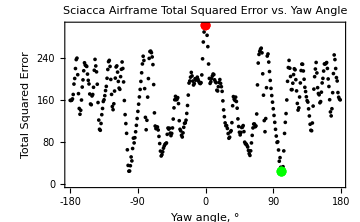

```mathematica
g102=Show[{g101,gbest,gworst},
ipad,
FrameTicks->{{Automatic,Automatic},{Range[-180,180,45],Automatic}}]
```

```mathematica
Export[dirData<>"scatter-error.pdf",g102]
```

/Users/dantopa/Mathematica_files/io/ert/mercury/snake/data/scatter-error.pdf

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```